```mathematica
Clear["Global`*"]
(*name="student@10.0.1.9://home/student/BEM/Kramer2021_0d03/result.json"*)
data01DLPF4=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/LPF4/01D_LPF4.txt"}],"Data"];
data01DFNPF1=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/FNPF1/01D_FNPF1.txt"}],"Data"];
data01DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/01D_CI95_Normalized.txt"}],"Data"];
data03DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/03D_Measured1_Normalized.txt"}],"Data"];
data05DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/05D_Measured1_Normalized.txt"}],"Data"];
name="~/BEM/Kramer2021_H00d03/result.json"
Quiet[data="float_COM"/.Import[name];];
Quiet[time="time"/.Import[name];];
(*Kramer20210d03=Import[NotebookDirectory[]<>"Kramer2021_0d3.csv"];*)
Z=data[[;;,3]];
H0=30/1000;
```

~/BEM/Kramer2021_H00d03/result.json

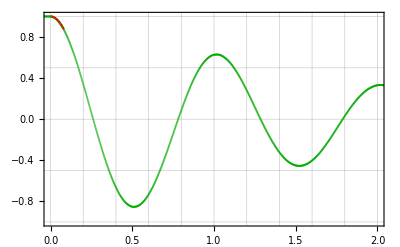

```mathematica
ListPlot[
{{#1(*/0.76*),#2(*/H0*)}&@@@data01DMeasured1Raw[[2;;]]
(*,{#1/0.76,#2/H0}&@@@data01DFNPF1[[2;;]],
{#1/0.76,#2/H0}&@@@data01DLPF4[[2;;]],*)
,{(time-0.05)/0.76,(Z-((*-34.8+*)900)/1000)/H0}ᵀ
},
PlotStyle->{{Darker[Green],Opacity[0.6]},{Red},{Dashed,Blue,Opacity[0.6]},{Thick}},
Joined->{False,True,True,True},
PlotRange->{{0,2},{-1.,1.}},
PlotTheme->"Scientific",
Frame->True,
Mesh->All,
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]}
]
```